# Setup

```mathematica
SetDirectory[NotebookDirectory[]];
Get["/Users/pcs/Desktop/Entropy/QMB_offline.wl"];
```

```mathematica
LaunchKernels[10]
```

{Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel,Local kernel}

```mathematica
Clear[haar];
haar[L_Integer]:=Normalize[Table[RandomVariate[NormalDistribution[]]+I RandomVariate[NormalDistribution[]],{2^L}]];
Clear[VNentropy];
VNentropy[0|0.]=0;
VNentropy[x_]:=-x*Log[x];
Clear[sdiag];
sdiag[L_,La_,Lb_,ini_]:=Module[{state=Dyad[ini],dima=2^(La),dimb=2^(Lb),rho},
rho=MatrixPartialTrace[state,2,{dima,dimb}];
Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]
];
Clear[svn];
svn[L_,La_,Lb_,ini_,eigenval_,eigenvec_,t_]:=Module[{state=StateEvolution[t,ini,eigenval,eigenvec],rho,λ,purity,dima=2^(La),dimb=2^(Lb),vn},
rho=MatrixPartialTrace[Dyad[state],2,{dima,dimb}];
Chop[Total[Map[VNentropy,Sort[Chop[Eigenvalues[rho]]]]]]
];
(*Define subsystem dimensions*)
(*Compute the Page value using the digamma function*)
pageEntropy[La_,Lb_]:=PolyGamma[0,(2^La)(2^Lb)+1]-PolyGamma[0,(2^Lb)+1]-((2^La)-1)/(2*(2^Lb));
```

# Open boundary conditions

```mathematica
L=10;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 528

Number of odd parity eigenvectors: 496

```mathematica
L=10;
g=1.0;
J=1;
h=1;
H=IsingNNOpenHamiltonian[h,g,J,L];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
```

```mathematica
ope=evenope+oddope;
```

```mathematica
parities=ParallelTable[Chop[Conjugate[i].ope.i],{i,eigenvec}];
```

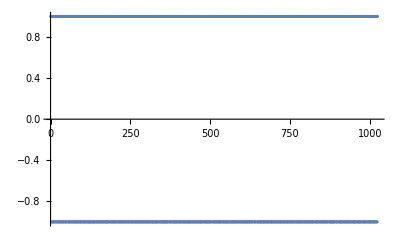

```mathematica
ListPlot[parities]
```

```mathematica
data=SortBy[Transpose[{parities,eigenval,eigenvec}],First];
```

```mathematica
neg=Count[data[[All,1]],_?Negative];
pos=Count[data[[All,1]],_?Positive];
```

```mathematica
MeanLevelSpacingRatio[data[[1;;neg,2]]]
MeanLevelSpacingRatio[data[[neg+1;;-1,2]]]
```

0.499916

0.526183

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[evenEigenvectors.H.ConjugateTranspose[evenEigenvectors],PlotRange->800,PlotTheme->"Detailed"]
MatrixPlot[oddEigenvectors.H.ConjugateTranspose[oddEigenvectors],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
evenH=evenEigenvectors.H.ConjugateTranspose[evenEigenvectors];
oddH=oddEigenvectors.H.ConjugateTranspose[oddEigenvectors];
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

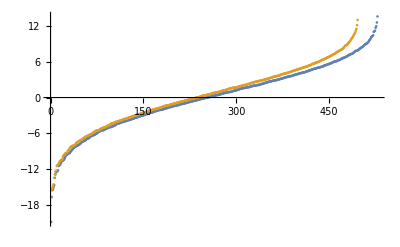

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All]
```

```mathematica
productstate2=Table[RandomChainProductState[L],3000];
iprs=ParallelTable[Quiet[Total[Abs[Conjugate[eigenvec].i]^4]],{i,productstate2},DistributedContexts->Full];
energies=ParallelTable[Chop[Conjugate[i].H.i],{i,productstate2},DistributedContexts->Full];
data=SortBy[Transpose[{iprs,energies,productstate2}],First];
```

```mathematica
productstates=data[[1;;50,3]];
productstates//Dimensions
```

{50,256}

```mathematica
La=L/2;
Lb=L-La;
```

```mathematica
tlist=Table[10^i,{i,-2,20,0.005}];
tlist//Length
```

4401

```mathematica
svntproduct=Table[ParallelTable[{t,svn[L,La,Lb,i,eigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full],{i,productstates}];
```

```mathematica
newenergies=data[[1;;Length[productstates],2]];
newiprs=data[[1;;Length[productstates],1]];
longmean=Table[Mean[svntproduct[[i]][[All,2]][[-500;;-1]]],{i,Length[productstates]}];
diagentropies=ParallelTable[sdiag[L,La,Lb,Conjugate[eigenvec].i],{i,productstates},DistributedContexts->Full];
alldata=Sort[Transpose[{newiprs,newenergies,diagentropies,longmean}],First];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
svnplots=ListLogLinearPlot[svntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Single RPS",Black,30]},PlotStyle->{Directive[Gray,Opacity[0.3]]}];
svnplotmean=ListLogLinearPlot[Mean[svntproduct],PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",20,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Mean RPS",Black,30]},PlotStyle->{Directive[Red,Opacity[1.0],PointSize[0.003]]}];
plot1=Show[{svnplots,svnplotmean,pageplot,LogLinearPlot[Mean[diagentropies],{x,tlist[[1]],tlist[[-1]]},PlotStyle->Directive[Orange,Dashed],PlotLegends->{Style["<Sd>",Black,30]}]},PlotRange->{All,All}]
```

-Graphics-

```mathematica
fakeeigenval=RandomReal[{-1,1},2^L];
fakesvntproduct=ParallelTable[{t,svn[L,La,Lb,productstates[[1]],fakeeigenval,eigenvec,t]},{t,tlist},DistributedContexts->Full];
fakelongmean=Mean[fakesvntproduct[[All,2]][[-500;;-1]]];
pageplot=LogLinearPlot[pageEntropy[La,Lb],{x,Min[tlist],Max[tlist]},PlotStyle->Directive[Dashed,Black],PlotLegends->{Style["Page value",Black,30]}];
fakesvnplot=ListLogLinearPlot[fakesvntproduct,PlotTheme->"Detailed",Joined->False,Axes->True,GridLines->None,PlotLabel->Style["L = "<>ToString[L]<>", La = "<>ToString[La]<>", J = "<>ToString[J]<>", h = "<>ToString[h]<>", g = "<>ToString[g]<>", Random product state",35,Black],FrameStyle->Directive[Black,FontSize->30],FrameLabel->{Style["t"],Style["Svn(t)"]},PlotRange->All,ImageSize->1000,PlotLegends->{Style["Fake evolution",Black,25]},PlotStyle->{Directive[Purple,Opacity[0.25]]}];
```

```mathematica
Show[{plot1,fakesvnplot}]
```

-Graphics-

# Closed boundary conditions

```mathematica
L=8;
```

```mathematica
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(* ==============================================*)
(*2. Construct the parity (reflection) operator*)
(* ==============================================*)
(*The parity operator P acts by reversing the order of the spins.That is,it sends a basis state|s1,s2,…,sL>to|sL,…,s2,s1>.*)
Pmatrix=SparseArray[Table[{i,basisIndex[Reverse[basis[[i]]]]}->1,{i,1,dim}],{dim,dim}];
(*It’s useful to check that Pmatrix is an involution (P^2=I)*)
Print["P^2 equals the identity? ",MatrixPower[Pmatrix,2]===IdentityMatrix[dim]];
(* ====================================================*)
(*3. Compute the eigenbasis of P and group sectors*)
(* ====================================================*)
(*Compute the eigenvalues and eigenvectors of the parity operator.Since Pmatrix is an involution,its eigenvalues are±1.*)
{vals,vecs}=Eigensystem[Pmatrix];
(*Collect the indices for each eigenvalue (using Chop to treat numerical zeros)*)
evenIndices=Flatten[Position[vals,x_/;Chop[x-1]==0]];
oddIndices=Flatten[Position[vals,x_/;Chop[x+1]==0]];
(*Extract the corresponding eigenvectors.Each vector is a column in ℂ^dim.*)
evenEigenvectors=vecs[[evenIndices]];
oddEigenvectors=vecs[[oddIndices]];
Print["Dimension of even parity sector: ",Length[evenEigenvectors]];
Print["Dimension of odd parity sector: ",Length[oddEigenvectors]];
```

P^2 equals the identity? False

Eigensystem::arhm: Because finding 256 out of the 256 eigenvalues and/or eigenvectors is likely to be faster with dense matrix methods, the sparse input matrix will be converted. If fewer eigenvalues and/or eigenvectors at machine precision would be sufficient, consider using N on the matrix and restricting this number using the second argument to Eigensystem.

Dimension of even parity sector: 136

Dimension of odd parity sector: 120

```mathematica
L=8;
g=0.01;
J=1;
h=1;
H=IsingNNClosedHamiltonian[h,g,J,L];
Clear[eigenval,eigenvec];
```

```mathematica
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

```mathematica
transform//Dimensions
H//Dimensions
```

{256,256}

{256,256}

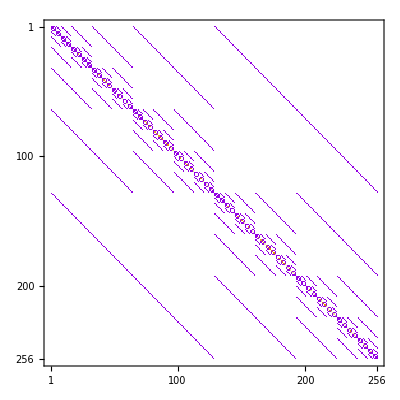

-Graphics-

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

```mathematica
evenH=evenEigenvectors.H.ConjugateTranspose[evenEigenvectors];
oddH=oddEigenvectors.H.ConjugateTranspose[oddEigenvectors];
```

```mathematica
{eveneigenval,eveneigenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddeigenval,oddeigenvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

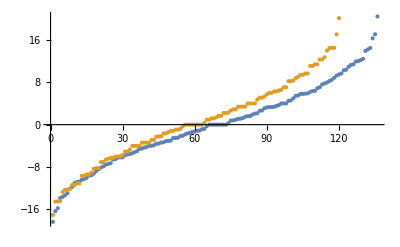

```mathematica
ListPlot[{eveneigenval,oddeigenval},PlotRange->All]
```

```mathematica
eveneigenvec//Dimensions
```

{136,136}

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
```

```mathematica
eveneigenvec//Dimensions
```

{136,136}

```mathematica
evenope//Dimensions
```

{256,256}

```mathematica
parities=ParallelTable[Chop[Conjugate[i].evenope.i],{i,eveneigenvec}];
```

Dot::dotsh: Tensors {0.0977281,0.117374,0.137671,0.158951,0.137671,0.0723886,0.176275,0.194455,0.117374,0.0568932,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.330338,-0.10185,-0.1361,0.210991,-0.1361,-0.00392302,0.0419563,0.193245,-0.10185,-0.0195442,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {5.54927×10^-17,0.112333,0.304272,-0.121458,-0.304272,-0.0404615,8.5832×10^-16,-0.1423,-0.112333,1.78309×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-1.15774×10^-15,0.16187,-0.100779,-0.0665159,0.100779,-0.0158684,5.83527×10^-16,-0.0178993,-0.16187,2.19235×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.0722779,0.0750035,-0.0359767,-0.0923342,-0.0359767,-0.04727,0.185421,-0.0902318,0.0750035,-0.00807185,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-2.144×10^-16,-0.043384,-0.0384448,0.0170391,0.0384448,-0.0476028,-4.5446×10^-16,0.00883843,0.043384,-3.36499×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.011531,0.0112775,0.0000191514,-0.00416509,0.0000191514,0.13233,0.00226355,-0.00146902,0.0112775,0.0488142,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-2.77065×10^-17,-0.00397549,0.00249789,0.000233046,-0.00249789,-0.170301,-2.5679×10^-16,-0.000122543,0.00397549,-2.31583×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.110102,-0.204558,0.0550441,-0.056126,0.0550441,-0.00922731,0.291719,0.169564,-0.204558,-0.114455,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.142881,0.060769,0.000252447,0.119249,0.000252447,0.015764,-0.111452,0.131697,0.060769,-0.029056,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {0.0977281,0.117374,0.137671,0.158951,0.137671,0.0723886,0.176275,0.194455,0.117374,0.0568932,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.330338,-0.10185,-0.1361,0.210991,-0.1361,-0.00392302,0.0419563,0.193245,-0.10185,-0.0195442,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {5.54927×10^-17,0.112333,0.304272,-0.121458,-0.304272,-0.0404615,8.5832×10^-16,-0.1423,-0.112333,1.78309×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-1.15774×10^-15,0.16187,-0.100779,-0.0665159,0.100779,-0.0158684,5.83527×10^-16,-0.0178993,-0.16187,2.19235×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.0722779,0.0750035,-0.0359767,-0.0923342,-0.0359767,-0.04727,0.185421,-0.0902318,0.0750035,-0.00807185,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-2.144×10^-16,-0.043384,-0.0384448,0.0170391,0.0384448,-0.0476028,-4.5446×10^-16,0.00883843,0.043384,-3.36499×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.011531,0.0112775,0.0000191514,-0.00416509,0.0000191514,0.13233,0.00226355,-0.00146902,0.0112775,0.0488142,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-2.77065×10^-17,-0.00397549,0.00249789,0.000233046,-0.00249789,-0.170301,-2.5679×10^-16,-0.000122543,0.00397549,-2.31583×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.110102,-0.204558,0.0550441,-0.056126,0.0550441,-0.00922731,0.291719,0.169564,-0.204558,-0.114455,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {0.142881,0.060769,0.000252447,0.119249,0.000252447,0.015764,-0.111452,0.131697,0.060769,-0.029056,«126»} have incompatible shapes.

Dot::dotsh: Tensors {0.0977281,0.117374,0.137671,0.158951,0.137671,0.0723886,0.176275,0.194455,0.117374,0.0568932,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.330338,-0.10185,-0.1361,0.210991,-0.1361,-0.00392302,0.0419563,0.193245,-0.10185,-0.0195442,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.112333,0.304272,-0.121458,-0.304272,-0.0404615,0,-0.1423,-0.112333,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.16187,-0.100779,-0.0665159,0.100779,-0.0158684,0,-0.0178993,-0.16187,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.0722779,0.0750035,-0.0359767,-0.0923342,-0.0359767,-0.04727,0.185421,-0.0902318,0.0750035,-0.00807185,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,-0.043384,-0.0384448,0.0170391,0.0384448,-0.0476028,0,0.00883843,0.043384,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.011531,0.0112775,0.0000191514,-0.00416509,0.0000191514,0.13233,0.00226355,-0.00146902,0.0112775,0.0488142,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,-0.00397549,0.00249789,0.000233046,-0.00249789,-0.170301,0,-0.000122543,0.00397549,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.110102,-0.204558,0.0550441,-0.056126,0.0550441,-0.00922731,0.291719,0.169564,-0.204558,-0.114455,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.142881,0.060769,0.000252447,0.119249,0.000252447,0.015764,-0.111452,0.131697,0.060769,-0.029056,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {-0.0171768,-0.0478601,0.0710213,-0.0404246,0.0710213,-0.0370953,-0.0909194,0.147693,-0.0478601,0.229184,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.0188429,-0.0119754,-0.0166959,-0.0707433,-0.0166959,0.00387833,0.107851,-0.0296694,-0.0119754,0.0327792,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00390487,-0.0219369,0.0285356,-0.00677113,0.0285356,-0.0773426,0.0638099,0.0729076,-0.0219369,-0.00653397,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.00395804,-0.00391807,-0.00391819,0.00282834,-0.00391819,-0.186362,0.00284542,-0.00439811,-0.00391807,0.0887719,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-1.72573×10^-10,0.00505959,-0.00505958,5.7563×10^-10,-0.00505958,0.248976,0.015096,-0.00241894,0.00505959,-0.00515464,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-3.19058×10^-17,0.0604108,-0.00538942,-0.0108624,0.00538942,0.0139016,-2.43369×10^-16,-0.0497593,-0.0604108,8.4246×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {1.27723×10^-15,0.00309172,0.000785161,-0.00713702,-0.000785161,0.100138,1.37482×10^-15,0.00518899,-0.00309172,-9.66187×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00293709,-0.0871428,0.0940646,-0.00329502,0.0940646,0.116452,-0.00880883,-0.0879024,-0.0871428,0.211513,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {3.40347×10^-16,0.0213358,-0.0865189,0.0599336,0.0865189,-0.108991,9.95469×10^-17,0.00967639,-0.0213358,-2.6301×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.0171768,-0.0478601,0.0710213,-0.0404246,0.0710213,-0.0370953,-0.0909194,0.147693,-0.0478601,0.229184,«126»} have incompatible shapes.

Dot::dotsh: Tensors {-2.35888×10^-16,-0.0420071,-0.0232575,-0.0483736,0.0232575,0.12724,-2.71378×10^-16,-0.0460103,0.0420071,1.60568×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {0.0188429,-0.0119754,-0.0166959,-0.0707433,-0.0166959,0.00387833,0.107851,-0.0296694,-0.0119754,0.0327792,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.00390487,-0.0219369,0.0285356,-0.00677113,0.0285356,-0.0773426,0.0638099,0.0729076,-0.0219369,-0.00653397,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {0.00395804,-0.00391807,-0.00391819,0.00282834,-0.00391819,-0.186362,0.00284542,-0.00439811,-0.00391807,0.0887719,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-1.72573×10^-10,0.00505959,-0.00505958,5.7563×10^-10,-0.00505958,0.248976,0.015096,-0.00241894,0.00505959,-0.00515464,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-3.19058×10^-17,0.0604108,-0.00538942,-0.0108624,0.00538942,0.0139016,-2.43369×10^-16,-0.0497593,-0.0604108,8.4246×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {1.27723×10^-15,0.00309172,0.000785161,-0.00713702,-0.000785161,0.100138,1.37482×10^-15,0.00518899,-0.00309172,-9.66187×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.00293709,-0.0871428,0.0940646,-0.00329502,0.0940646,0.116452,-0.00880883,-0.0879024,-0.0871428,0.211513,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {3.40347×10^-16,0.0213358,-0.0865189,0.0599336,0.0865189,-0.108991,9.95469×10^-17,0.00967639,-0.0213358,-2.6301×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {-0.0171768,-0.0478601,0.0710213,-0.0404246,0.0710213,-0.0370953,-0.0909194,0.147693,-0.0478601,0.229184,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-2.35888×10^-16,-0.0420071,-0.0232575,-0.0483736,0.0232575,0.12724,-2.71378×10^-16,-0.0460103,0.0420071,1.60568×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {0.0188429,-0.0119754,-0.0166959,-0.0707433,-0.0166959,0.00387833,0.107851,-0.0296694,-0.0119754,0.0327792,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00390487,-0.0219369,0.0285356,-0.00677113,0.0285356,-0.0773426,0.0638099,0.0729076,-0.0219369,-0.00653397,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.00395804,-0.00391807,-0.00391819,0.00282834,-0.00391819,-0.186362,0.00284542,-0.00439811,-0.00391807,0.0887719,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-1.72573×10^-10,0.00505959,-0.00505958,5.7563×10^-10,-0.00505958,0.248976,0.015096,-0.00241894,0.00505959,-0.00515464,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.0604108,-0.00538942,-0.0108624,0.00538942,0.0139016,0,-0.0497593,-0.0604108,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.00309172,0.000785161,-0.00713702,-0.000785161,0.100138,0,0.00518899,-0.00309172,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00293709,-0.0871428,0.0940646,-0.00329502,0.0940646,0.116452,-0.00880883,-0.0879024,-0.0871428,0.211513,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.0213358,-0.0865189,0.0599336,0.0865189,-0.108991,0,0.00967639,-0.0213358,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {0,-0.0420071,-0.0232575,-0.0483736,0.0232575,0.12724,0,-0.0460103,0.0420071,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {-0.0048702,0.00745343,0.00706212,-0.00377032,0.00706212,-0.11636,-0.0063723,0.00592945,0.00745343,0.0465139,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-3.42605×10^-17,-0.0206748,0.0494913,-0.0555566,-0.0494913,0.0925275,3.68091×10^-17,0.0523186,0.0206748,-7.23×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.0449603,-0.0750399,-0.079338,0.0815483,-0.079338,0.0381807,0.0936383,-0.0265955,-0.0750399,0.130733,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00808529,0.0284067,0.000426769,-0.0137941,0.000426769,0.0909135,-0.0584005,-0.0151154,0.0284067,-0.0945973,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00538052,-0.0169314,0.0377947,-0.0176276,0.0377947,0.00854466,-0.0479309,0.00788664,-0.0169314,0.0877025,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-7.21275×10^-17,0.00401722,-0.0080413,-0.0214981,0.0080413,0.035316,-1.90022×10^-16,0.00353393,-0.00401722,-1.18031×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.000132077,0.000278147,0.00030223,-0.000656278,0.00030223,0.0687012,-0.000291505,0.000206909,0.000278147,-0.135894,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00862245,0.0217836,0.0196263,-0.0127646,0.0196263,-0.0131944,-0.0470405,0.031037,0.0217836,0.0117669,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-1.55112×10^-17,0.00452851,-0.00154842,-0.0136922,0.00154842,0.0477823,-4.27013×10^-17,-0.0140213,-0.00452851,-3.53217×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.0048702,0.00745343,0.00706212,-0.00377032,0.00706212,-0.11636,-0.0063723,0.00592945,0.00745343,0.0465139,«126»} have incompatible shapes.

Dot::dotsh: Tensors {-2.00718×10^-18,0.00712278,0.00492013,0.0066844,-0.00492013,-0.0337962,3.0717×10^-17,0.00279564,-0.00712278,1.19513×10^-16,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-3.42605×10^-17,-0.0206748,0.0494913,-0.0555566,-0.0494913,0.0925275,3.68091×10^-17,0.0523186,0.0206748,-7.23×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {0.0449603,-0.0750399,-0.079338,0.0815483,-0.079338,0.0381807,0.0936383,-0.0265955,-0.0750399,0.130733,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.00808529,0.0284067,0.000426769,-0.0137941,0.000426769,0.0909135,-0.0584005,-0.0151154,0.0284067,-0.0945973,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.00538052,-0.0169314,0.0377947,-0.0176276,0.0377947,0.00854466,-0.0479309,0.00788664,-0.0169314,0.0877025,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-7.21275×10^-17,0.00401722,-0.0080413,-0.0214981,0.0080413,0.035316,-1.90022×10^-16,0.00353393,-0.00401722,-1.18031×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.000132077,0.000278147,0.00030223,-0.000656278,0.00030223,0.0687012,-0.000291505,0.000206909,0.000278147,-0.135894,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-0.00862245,0.0217836,0.0196263,-0.0127646,0.0196263,-0.0131944,-0.0470405,0.031037,0.0217836,0.0117669,«126»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-1.55112×10^-17,0.00452851,-0.00154842,-0.0136922,0.00154842,0.0477823,-4.27013×10^-17,-0.0140213,-0.00452851,-3.53217×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {-0.0048702,0.00745343,0.00706212,-0.00377032,0.00706212,-0.11636,-0.0063723,0.00592945,0.00745343,0.0465139,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {-2.00718×10^-18,0.00712278,0.00492013,0.0066844,-0.00492013,-0.0337962,3.0717×10^-17,0.00279564,-0.00712278,1.19513×10^-16,«126»} have incompatible shapes.

Dot::dotsh: Tensors {0,-0.0206748,0.0494913,-0.0555566,-0.0494913,0.0925275,0,0.0523186,0.0206748,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0.0449603,-0.0750399,-0.079338,0.0815483,-0.079338,0.0381807,0.0936383,-0.0265955,-0.0750399,0.130733,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00808529,0.0284067,0.000426769,-0.0137941,0.000426769,0.0909135,-0.0584005,-0.0151154,0.0284067,-0.0945973,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00538052,-0.0169314,0.0377947,-0.0176276,0.0377947,0.00854466,-0.0479309,0.00788664,-0.0169314,0.0877025,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.00401722,-0.0080413,-0.0214981,0.0080413,0.035316,0,0.00353393,-0.00401722,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.000132077,0.000278147,0.00030223,-0.000656278,0.00030223,0.0687012,-0.000291505,0.000206909,0.000278147,-0.135894,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {-0.00862245,0.0217836,0.0196263,-0.0127646,0.0196263,-0.0131944,-0.0470405,0.031037,0.0217836,0.0117669,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {0,0.00452851,-0.00154842,-0.0136922,0.00154842,0.0477823,0,-0.0140213,-0.00452851,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {0,0.00712278,0.00492013,0.0066844,-0.00492013,-0.0337962,0,0.00279564,-0.00712278,0,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

Dot::dotsh: Tensors {0.0977281,0.117374,0.137671,0.158951,0.137671,0.0723886,0.176275,0.194455,0.117374,0.0568932,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

Dot::dotsh: Tensors {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} and {0.0977281,0.117374,0.137671,0.158951,0.137671,0.0723886,0.176275,0.194455,0.117374,0.0568932,«126»} have incompatible shapes.

Dot::dotsh: Tensors {0.208297,0.198997,0.238834,0.197378,0.238834,0.0858203,0.226393,0.136179,0.198997,0.0681261,«126»} and {{1,0,0,0,0,0,0,0,0,0,«246»},{0,1,0,0,0,0,0,0,0,0,«246»},{0,0,1,0,0,0,0,0,0,0,«246»},{0,0,0,1,0,0,0,0,0,0,«246»},{0,0,0,0,1,0,0,0,0,0,«246»},{0,0,0,0,0,1,0,0,0,0,«246»},{0,0,0,0,0,0,1,0,0,0,«246»},{0,0,0,0,0,0,0,1,0,0,«246»},{0,0,0,0,0,0,0,0,1,0,«246»},{0,0,0,0,0,0,0,0,0,1,«246»},«246»} have incompatible shapes.

General::stop: Further output of Dot::dotsh will be suppressed during this calculation.

# Parity eigenvectors

```mathematica
L=10;
```

```mathematica
Clear[evenEigenvectors,oddEigenvectors];
basis=Tuples[{0,1},L];
(*dim=2^L*)
dim=Length[basis];  
(*Create an association to map each basis state to an index*)
basisIndex=AssociationThread[basis,Range[dim]];
(*Step 3:Define a function to convert a basis state into a Hilbert space vector*)
basisVector[state_]:=SparseArray[{basisIndex[state]->1},{dim}];
(*Step 4:Initialize containers for eigenvectors and bookkeeping*)
evenEigenvectors={};  (*Will store even (symmetric) eigenvectors*)
oddEigenvectors={};   (*Will store odd (antisymmetric) eigenvectors*)
processed=ConstantArray[False,dim];  (*Marks which basis states are processed*)
(*Function to compute the reversed state (parity operation on configuration)*)
reverseState[s_List]:=Reverse[s];
(*Step 5:Loop over basis to construct eigenvectors*)
Do[If[processed[[i]],Continue[]];(*Skip states already processed*)(*Retrieve current state and its Hilbert space vector*)state=basis[[i]];
u=basisVector[state];
(*Compute its reflected (reversed) state and corresponding vector*)revState=reverseState[state];
pos=basisIndex[revState];
v=basisVector[revState];
If[i==pos,(*Case:state invariant under parity;already an eigenvector with eigenvalue+1*)
AppendTo[evenEigenvectors,u],(*Case:state and its reflected partner are different.Construct symmetric and antisymmetric combinations*)
symVec=(u+v)/Sqrt[2];
antiVec=(u-v)/Sqrt[2];
AppendTo[evenEigenvectors,symVec];
AppendTo[oddEigenvectors,antiVec];
(*Mark both states as processed*)processed[[i]]=True;
processed[[pos]]=True;];
(*Ensure the current state is marked as processed if not already*)processed[[i]]=True;,{i,1,dim}];
(*Step 6:Report the dimensions (the number of eigenvectors in each parity sector)*)
Print["Number of even parity eigenvectors: ",Length[evenEigenvectors]];
Print["Number of odd parity eigenvectors: ",Length[oddEigenvectors]];
```

Number of even parity eigenvectors: 528

Number of odd parity eigenvectors: 496

```mathematica
g=1;
J=1;
h=1.0;
H=IsingNNClosedHamiltonian[h,g,J,L];
```

```mathematica
transform=Join[evenEigenvectors,oddEigenvectors];
```

```mathematica
MatrixPlot[H,PlotRange->800]
MatrixPlot[transform.H.ConjugateTranspose[transform],PlotRange->800,PlotTheme->"Detailed"]
```

-Graphics-

-Graphics-

```mathematica
evenope=Sum[Dyad[i],{i,evenEigenvectors}];
oddope=Sum[-Dyad[i],{i,oddEigenvectors}];
ope=evenope+oddope;
```

```mathematica
newH=transform.H.ConjugateTranspose[transform];
```

```mathematica
newH//Dimensions
```

{1024,1024}

```mathematica
evenEigenvectors//Length
oddEigenvectors//Length
```

528

496

```mathematica
evenH=newH[[1;;Length[evenEigenvectors],1;;Length[evenEigenvectors]]];
oddH=newH[[Length[evenEigenvectors]+1;;-1,Length[evenEigenvectors]+1;;-1]];
evenH//Dimensions
oddH//Dimensions
```

{528,528}

{496,496}

```mathematica
MatrixPlot[evenH]
MatrixPlot[oddH]
```

-Graphics-

-Graphics-

```mathematica
{evenval,evenvec}=Transpose[Sort[Transpose[Eigensystem[evenH]]]];
{oddval,oddvec}=Transpose[Sort[Transpose[Eigensystem[oddH]]]];
```

```mathematica
MeanLevelSpacingRatio[evenval]
MeanLevelSpacingRatio[oddval]
```

0.412485

0.39634

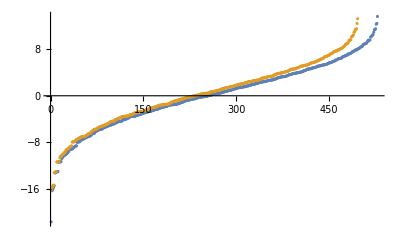

```mathematica
ListPlot[{evenval,oddval},PlotRange->All]
```

```mathematica
g=1;
J=1;
h=1.0;
H=IsingNNClosedHamiltonian[h,g,J,L];
{eigenval,eigenvec}=Transpose[Sort[Transpose[Eigensystem[H]]]];
```